```mathematica
Quit
```

```mathematica
(*Ridefinisco le funzioni Arg e Abs*)
Unprotect[Arg];
Arg[x + I y]:= ArcTan[x,y];
Unprotect[Abs];
Abs[x + I y]:= Sqrt[x^2 + y^2];

(*La funzione ToReal mi restituisce le parti reale e immaginaria del numero complesso (z) inserito*)
Clear[ToReal]
ToReal[exp_, z_,{x_,y_}]:= 
Module[{exprep=ReplaceAll[exp, z:>x+ I y]},ComplexExpand[{Re[exprep],Im[exprep]}]]
ToReal[exp_]:=ToReal[exp,z,{x,y}]

(*La funzione RealFunction mi restituisce le parti reale e immaginaria della funzione inserita*)
Clear[RealFunction]
RealFunction[f_][s_,t_]:=ToReal[f,z,{s,t}]

(*La funzione GradRe mi restiutuisce il gradiente della parte reale della funzione inserita*)
Clear[GradRe]
GradRe[exp_,z_,{x_,y_}]:= Grad[ToReal[exp,z,{x,y}][[1]],{x,y}]
GradRe[exp_]:= GradRe[exp,z,{x,y}]


(*Con la funzione StreamCurve trovo le curve integrali relative alle equazioni differenziali x'(t)=X(x(t)) e y'(t)=Y(y(t)), al variare di t in (t1, t2), con condizoni iniziali x(t0)=x0 e y(t0)=y0.*)
(*Il campo vettoriale (X(x,y), Y(x,y)) è dato come input a StreamCurve tramite una lista con due argomenti (è la variabile vect)*)
(*Si possono dare le opzioni NDSolve tramite la variabile opts*)
(*L'output di StreamCurve è una lista di due argomenti in cui ogni argomento è una regola di sostituzione*)
Clear[StreamCurve]
StreamCurve[vect_,{x_,y_},{x0_,y0_},{t_,t1_,t2_},opts___]:= 
Flatten[NDSolve[{x'[t]==ReplaceAll[vect[[1]],{x:>x[t],y:>y[t]}],y'[t]==ReplaceAll[vect[[2]],{x:>x[t],y:>y[t]}],x[0]==x0, y[0]==y0},{x,y},{t,t1,t2},opts]]

(*Flussox e Flussoy sono due funzioni di una variabile che forniscono una curva integrale del gradiente della parte reale di una funzione olomorfa f(z)*)
(*L'input è dato da: la funzione f(z) (ma solo il nome f, non la z!), la condizione iniziale (x0,y0) della curva, l'intervallo di tempo tmin e tmax*)
Flussox[f_,{x0_,y0_},tmin_,tmax_][s_]:=x[s]//.StreamCurve[GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[1]]
Flussoy[f_,{x0_,y0_},tmin_,tmax_][s_]:=y[s]//.StreamCurve[GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[2]]

(*La funzione DeterminaTempoMinMax serve a determinare l'intervallo di tempo in cui la curva integrale è ben definita e si trova all'interno del rettangolo individuato da xMin, xMax, yMin, yMax. Come input prende la funzione, le condizioni iniziali, il rettangolo di definizione e il tempo massimo raggiungibile (serve per non iterare all'infinito). L'output contiene l'intervallo di tempo di definizione e la funzione parametrizzata in due variabili (reale e immaginaria nel piano complesso)*)
Clear[DeterminaTempoMinMax]
DeterminaTempoMinMax[f_,cond_,xMax_,xMin_,yMax_,yMin_,tMax_]:= Module[{temp},
tabellaTempieFunz=Table[{{0,0},{0,0}},{i,1,Length[cond]}];
For[j=1,j<=Length[cond],j=j+1,{
	temp=0;
	(*Calcolo t2 e t1*)
For[l=1,l>-1.5,l-=2,{
temp=0;
	For[k=1000*l,k!= 0.001*l,k=k/10,{For[i=0,((Check[StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]],$Failed] === $Failed)===False)&&((Check[StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]],$Failed] === $Failed)===False)&& ((x//.{StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]<xMax) && ((y//.{StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]<yMax) &&((x//.{StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]>xMin) && ((y//.{StreamCurve[GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]>yMin) &&(Abs[temp+k]<tMax),i++,{temp+=k}]}];
tabellaTempieFunz[[j]][[1]][[l/2+1.5]]=temp;tabellaTempieFunz[[j]][[2]][[1]]=Flussox[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s];tabellaTempieFunz[[j]][[2]][[2]]=Flussoy[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s]}];}];
	Return[tabellaTempieFunz];
]



(***********************************************************)


(*PlotLineeDiFlusso disegna una collezione di curve integrali date dalla parte reale della funzione f con condizioni dati dalla lista tabellatempi*)
(*Per usare questa funzione, deve essere definita 1) la funzione complessa da passare in input, 2) una tabella di condizioni (da determinare con la funzione DeterminaTempoMinMax), 3) eventuali opzioni per il grafico*) 
Clear[PlotLineeDiFlusso]
PlotLineeDiFlusso[tabellatempi_,opts___]:=Show[Table[ParametricPlot[tabellatempi[[i]][[2]],{s,tabellatempi[[i]][[1]][[1]],tabellatempi[[i]][[1]][[2]]},opts,PlotRange->All],{i,1,Length[tabellatempi]}]]

Clear[PlotLineeDiFlussoRuotate]
PlotLineeDiFlussoRuotate[tabellatempi_,a_,opts___]:=Show[Table[ParametricPlot[tabellatempi[[i]][[2]].{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}},{s,tabellatempi[[i]][[1]][[1]],tabellatempi[[i]][[1]][[2]]},opts,PlotRange->All],{i,1,Length[tabellatempi]}]]


(*Frecce*)
Clear[PlotLineeDiFlussoFrecce]
PlotLineeDiFlussoFrecce[tabellatempi_,scarto_,dimfrecce_,opts___]:=Module[{tempor,frecce,a},
frecce={};
tempor={};
For[i=1,i<=Length[tabellatempi],i++,{For[j=tabellatempi[[i,1,1]]+0.001,j<=tabellatempi[[i,1,2]],j+=scarto,{
s=j-0.001;
tempor=tabellatempi[[i,2]];
s+=0.001;
tempor=Arrow[{tempor,tabellatempi[[i,2]]}];
frecce=Join[frecce,{tempor}];
}];}];
Clear[s];
a=Show[PlotLineeDiFlusso[tabellatempi,opts]];
Return[Show[a,Graphics[{Arrowheads[dimfrecce],frecce}]]]
]

Clear[PlotLineeDiFlussoFrecceRuotate]
PlotLineeDiFlussoFrecceRuotate[tabellatempi_,scarto_,dimfrecce_,r_,opts___]:=Module[{tempor,frecce,a},
frecce={};
tempor={};
For[i=1,i<=Length[tabellatempi],i++,{For[j=tabellatempi[[i,1,1]]+0.001,j<=tabellatempi[[i,1,2]],j+=scarto,{
s=j-0.001;
tempor=tabellatempi[[i,2]].{{Cos[r],-Sin[r]},{Sin[r],Cos[r]}};
s+=0.001;
tempor=Arrow[{tempor,tabellatempi[[i,2]].{{Cos[r],-Sin[r]},{Sin[r],Cos[r]}}}];
frecce=Join[frecce,{tempor}];
}];}];
Clear[s];
a=Show[PlotLineeDiFlussoRuotate[tabellatempi,r,opts]];
Return[Show[a,Graphics[{Arrowheads[dimfrecce],frecce}]]]
]


(*La funzione MT è la funzione di Milne-Thomson applicata alla funzione p considerando un disco di centro q e raggio a*)
Clear[MT]
MT[p_,q_,a_][z_]:=p[z]+Conjugate[p[((a^2)/(Conjugate[(z-q)]))+q]]

(*La funzione colore è utilizzata nelle animazioni per far scomparire i pallini una volta raggiunto il bordo del rettangolo di definizione. Prende in input un istante di tempo l e un vettore contenente il tempo massimo e minimo globale*)
Clear[colore]
colore[l_,tempiminmax_]:= Module[{color},If[tempiminmax[[1]]<l<tempiminmax[[2]],color=Black, color=White];Return[color];]

(*La funzione Joukamento è la trasformazione di Joukowski*)
Joukamento[z_]:=1/2(z+1/z);
JoukamentoRot[z_,a_]:=Joukamento[Exp[I*a]*z];


(*Le funzioni InvJouko1 e InvJouko2 sono le due possibilità della funzione inversa della Joukowski*)
Clear[InvJouko1]
Clear[InvJouko2]
InvJouko1[x_,y_]:={x+(4 x^2 y^2+(-1+x^2-y^2)^2)^(1/4) Cos[1/2 ArcTan[-1+x^2-y^2,2x*y]],(y+(4 x^2 y^2+(-1+x^2-y^2)^2)^(1/4) Sin[1/2 ArcTan[-1+x^2-y^2,2x*y]])}
InvJouko2[x_,y_]:={x-(4 x^2 y^2+(-1+x^2-y^2)^2)^(1/4) Cos[1/2 ArcTan[-1+x^2-y^2,2x*y]],(y-(4 x^2 y^2+(-1+x^2-y^2)^2)^(1/4) Sin[1/2 ArcTan[-1+x^2-y^2,2x*y]])}

InvJouko1Rot[x_,y_,a_]:=InvJouko1[Cos[a]x-Sin[a]y,Sin[a]x+Cos[a]y];

(*Le matrici JacobiJouko1 e JacobiJouko2 sono le matrici jacobiane delle due funzioni inverse InvJouko1 e InvJouko2*)
JacobiJouko1[x_,y_]:={{D[InvJouko1[x,y][[1]],x],D[InvJouko1[x,y][[1]],y]},{D[InvJouko1[x,y][[2]],x],D[InvJouko1[x,y][[2]],y]}}
JacobiJouko2[x_,y_]:={{D[InvJouko2[x,y][[1]],x],D[InvJouko2[x,y][[1]],y]},{D[InvJouko2[x,y][[2]],x],D[InvJouko2[x,y][[2]],y]}}

(*Jouko1GradRe e Jouko2GradRe sono la funzione GradRe applicata a jexp composta con la Joukowski invertita*)
Jouko1GradRe[jexp_]:=(GradRe[jexp,z,{x1,y1}]//.{x1->InvJouko1[x,y][[1]],y1->InvJouko1[x,y][[2]]}).JacobiJouko1[x,y]
Jouko2GradRe[jexp_]:=(GradRe[jexp,z,{x1,y1}]//.{x1->InvJouko2[x,y][[1]],y1->InvJouko2[x,y][[2]]}).JacobiJouko2[x,y]

(*Le seguenti funzioni sono le funzioni Flussox e Flussoy con Jouko1GradRe e Jouko2GradRe a posto di GradRe*)
Jouko1Flussox[f_,{x0_,y0_},tmin_,tmax_][s_]:=x[s]//.StreamCurve[Jouko1GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[1]]
Jouko1Flussoy[f_,{x0_,y0_},tmin_,tmax_][s_]:=y[s]//.StreamCurve[Jouko1GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[2]]
Jouko2Flussox[f_,{x0_,y0_},tmin_,tmax_][s_]:=x[s]//.StreamCurve[Jouko2GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[1]]
Jouko2Flussoy[f_,{x0_,y0_},tmin_,tmax_][s_]:=y[s]//.StreamCurve[Jouko2GradRe[f[z]],{x,y},{x0,y0},{t,tmin,tmax}][[2]]

(*Le seguenti funzioni sono la funzione DeterminaTempoMinMax che utilzza la riscrittura delle funzioni Flussox, Flussoy e GradRe adattate alla trasformazione di Joukowski*)
(*La prima funzione lavora andando in avanti nel tempo e per x>=0, la seconda funzione lavora andando indietro nel tempo e per x<=0*)
Clear[Jouko1DeterminaTempoMinMax]
Jouko1DeterminaTempoMinMax[f_,cond_,xMax_,xMin_,yMax_,yMin_,tMax_]:= Module[{temp},
tabellaTempieFunz=Table[{{0,0},{0,0}},{i,1,Length[cond]}];
For[j=1,j<=Length[cond],j=j+1,{
	temp=0;
	(*Calcolo t2 e t1*)
For[l=1,l>-1.5,l-=8,{
temp=0;
	For[k=1000*l,k!= 0.001*l,k=k/10,{For[i=0,((Check[StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]],$Failed] === $Failed)===False)&&((Check[StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]],$Failed] === $Failed)===False)&& ((x//.{StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]<xMax) && ((y//.{StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]<yMax) &&((x//.{StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]>xMin) && ((y//.{StreamCurve[Jouko1GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]>yMin) &&(Abs[temp+k]<tMax),i++,{temp+=k}]}];
tabellaTempieFunz[[j]][[1]][[l/2+1.5]]=temp;tabellaTempieFunz[[j]][[2]][[1]]=Jouko1Flussox[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s];tabellaTempieFunz[[j]][[2]][[2]]=Jouko1Flussoy[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s]}];}];
	Return[tabellaTempieFunz];
]

Clear[Jouko2DeterminaTempoMinMax]
Jouko2DeterminaTempoMinMax[f_,cond_,xMax_,xMin_,yMax_,yMin_,tMax_]:= Module[{temp},
tabellaTempieFunz=Table[{{0,0},{0,0}},{i,1,Length[cond]}];
For[j=1,j<=Length[cond],j=j+1,{
	temp=0;
	(*Calcolo t2 e t1*)
For[l=-1,l>-1.5,l-=2,{
temp=0;
	For[k=1000*l,k!= 0.001*l,k=k/10,{For[i=0,((Check[StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]],$Failed] === $Failed)===False)&&((Check[StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]],$Failed] === $Failed)===False)&& ((x//.{StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]<xMax) && ((y//.{StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]<yMax) &&((x//.{StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[1]]})[temp+k]>xMin) && ((y//.{StreamCurve[Jouko2GradRe[f[z]],{x,y},cond[[j]],{t,0,temp+k}][[2]]})[temp+k]>yMin) &&(Abs[temp+k]<tMax),i++,{temp+=k}]}];
tabellaTempieFunz[[j]][[1]][[l/2+1.5]]=temp;tabellaTempieFunz[[j]][[2]][[1]]=Jouko2Flussox[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s];tabellaTempieFunz[[j]][[2]][[2]]=Jouko2Flussoy[f,cond[[j]],tabellaTempieFunz[[j]][[1]][[1]],tabellaTempieFunz[[j]][[1]][[2]]][s]}];}];
	Return[tabellaTempieFunz];
]

(*La funzione JoukoDeterminaTempoMinMax definisce come funzione a tratti la funzione DeterminaTempoMinMax adattata alla trasformazione di Joukowski per ogni x*)
Clear[JoukoDeterminaTempoMinMax]
JoukoDeterminaTempoMinMax[f_,cond_,xMax_,xMin_,yMax_,yMin_,tMax_]:=Module[{temp},
tabellaTempieFunz2=Jouko1DeterminaTempoMinMax[f,cond,xMax,0,yMax,yMin,tMax];
tabellaTempieFunz1=Jouko2DeterminaTempoMinMax[f,cond,0,xMin,yMax,yMin,tMax];
tabella=Table[{{tabellaTempieFunz1[[i,1,1]],tabellaTempieFunz2[[i,1,2]]},{Piecewise[{{tabellaTempieFunz1[[i,2,1]],s<0},{tabellaTempieFunz2[[i,2,1]],s>0}}],Piecewise[{{tabellaTempieFunz1[[i,2,2]],s<0},{tabellaTempieFunz2[[i,2,2]],s>0}}]}},{i,1,Length[cond]}];
Return[tabella]];
```

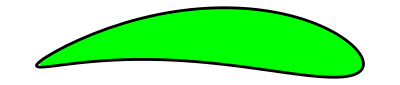

```mathematica
(*Disegno del profilo alare colorato*)
ProfiloAlare=Show[Region[Style[ParametricRegion[{r*ToReal[Joukamento[0.1+0.22 I+1.2Exp[I t]]][[1]]-(1-r)*0.3,r*ToReal[Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[2]]+(1-r)*0.2},{{t,0,2Pi},{r,0,1}}],Green]],ParametricPlot[{ToReal[Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[1]],ToReal[Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[2]]},{t,0,2Pi},AspectRatio->Automatic,AxesOrigin->{0,0},ColorFunction->Function[{t},Black]]]
```

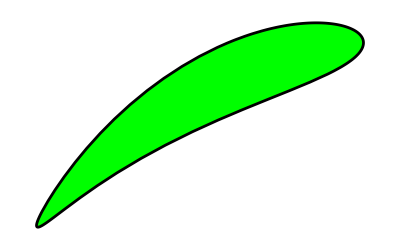

```mathematica
ProfiloAlareRuotato=Show[Region[Style[ParametricRegion[{r*ToReal[Exp[I*(Pi/6)]*Joukamento[0.1+0.22 I+1.2Exp[I t]]][[1]]-(1-r)*0.02,r*ToReal[Exp[I*(Pi/6)]*Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[2]]+(1-r)*0.35},{{t,0,2Pi},{r,0,1}}],Green]],ParametricPlot[{ToReal[Exp[I*(Pi/6)]*Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[1]],ToReal[Exp[I*(Pi/6)]*Joukamento[0.1+0.22 I+1.2 Exp[I t]]][[2]]},{t,0,2Pi},AspectRatio->Automatic,AxesOrigin->{0,0},ColorFunction->Function[{t},Black]]]
```

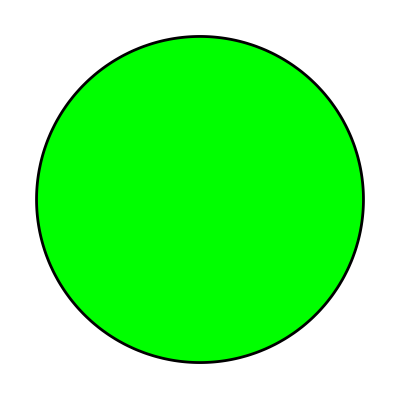

```mathematica
(*Disegno del profilo alare colorato*)
JoukoDisco=Show[Region[Style[ParametricRegion[{0.1+r*Cos[t],0.22+r*Sin[t]},{{t,0,2Pi},{r,0,1.2}}],Green]],ParametricPlot[{0.1+1.2*Cos[t],0.22+1.2*Sin[t]},{t,0,2Pi},AspectRatio->Automatic,AxesOrigin->{0,0},ColorFunction->Function[{t},Black]]]
```